```mathematica
SetDirectory@NotebookDirectory[]
```

C:\Users\John\SkyDrive\Documents\Task\NegPolaron

```mathematica
SetDirectory["C:\\Users\\John\\SkyDrive\\Documents\\Task\\AllTheory"]
```

C:\Users\John\SkyDrive\Documents\Task\AllTheory

```mathematica
config=Import["config.dat"];
```

```mathematica
asize=23;
```

```mathematica
p[1]=ListPlot3D[config[[1;;80,All]],PlotRange->All,DataRange->{{0,200},{1,800}},Mesh->10,ColorFunctionScaling->True,Lighting->Automatic,PlotStyle->Opacity[0.8],ColorFunction->Function[{x,y,z},ColorData[{"Rainbow","Reverse"}][Rescale[z,{0,0.9}]]]]
```

-Graphics3D-

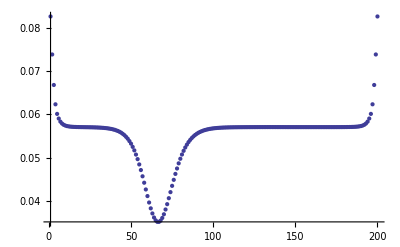

```mathematica
ListPlot[config[[10]],PlotRange->All]
```

```mathematica
phiToU[x_List]:=x*Array[If[Mod[#1,2]==0,1,-1]&,Length[x],1]
```

```mathematica
Dimensions[config]
```

{100,200}

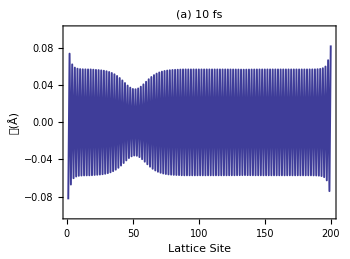

```mathematica
fa[1]=ListPlot[phiToU[config[[1,1;;200]]],PlotStyle->Directive[Thickness[0.004]],PlotRange->{All,{-0.1,0.1}},Joined->True,Axes->False,Frame->True,FrameStyle->Directive[Thickness[0.006],FontSize->asize],ImageSize->350,FrameLabel->(Style[#1,Bold,asize]&/@{"Lattice Site","𝓊(Å)"}),AspectRatio->0.74,PlotLabel->Style["(a) 10 fs",Bold,asize]]
```

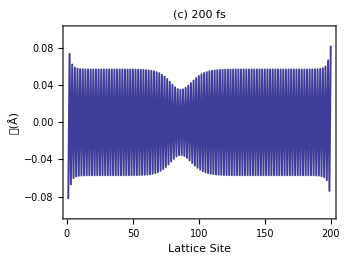

```mathematica
fa[2]=ListPlot[phiToU[config[[20,1;;200]]],PlotStyle->Directive[Thickness[0.004]],PlotRange->{All,{-0.1,0.1}},Joined->True,Axes->False,Frame->True,FrameStyle->Directive[Thickness[0.006],FontSize->asize],ImageSize->350,FrameLabel->(Style[#1,Bold,asize]&/@{"Lattice Site","𝓊(Å)"}),AspectRatio->0.74,PlotLabel->Style["(c) 200 fs",Bold,asize]]
```

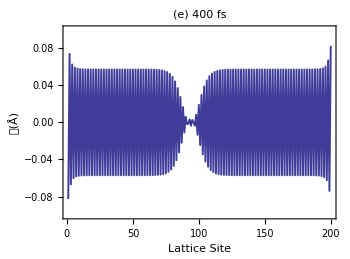

```mathematica
fa[3]=ListPlot[phiToU[config[[40,1;;200]]],PlotStyle->Directive[Thickness[0.004]],PlotRange->{All,{-0.1,0.1}},Joined->True,Axes->False,Frame->True,FrameStyle->Directive[Thickness[0.006],FontSize->asize],ImageSize->350,FrameLabel->(Style[#1,Bold,asize]&/@{"Lattice Site","𝓊(Å)"}),AspectRatio->0.74,PlotLabel->Style["(e) 400 fs",Bold,asize]]
```

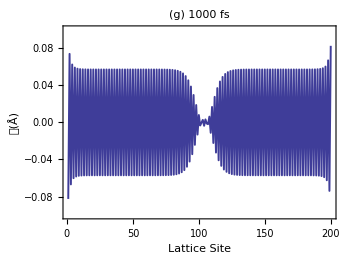

```mathematica
fa[4]=ListPlot[phiToU[config[[100,1;;200]]],PlotStyle->Directive[Thickness[0.004]],PlotRange->{All,{-0.1,0.1}},Joined->True,Axes->False,Frame->True,FrameStyle->Directive[Thickness[0.006],FontSize->asize],ImageSize->350,FrameLabel->(Style[#1,Bold,asize]&/@{"Lattice Site","𝓊(Å)"}),AspectRatio->0.74,PlotLabel->Style["(g) 1000 fs",Bold,asize]]
```

```mathematica
ListPlot[phiToU[config[[40,1;;200]]],Joined->True,PlotRange->All]
```

color stands for the distance Hue[distance]

```mathematica
Array[#1&,50,{0,1.}]
```

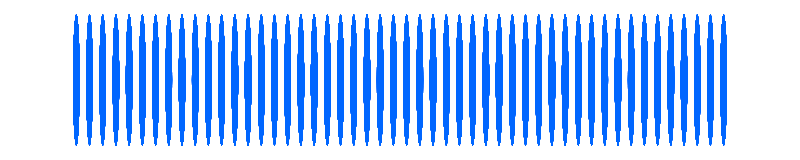

```mathematica
Graphics[Array[{Hue[#2/10.],Disk[{#1,0},2]}&,{50,50},{{0,400.},{6.,6.}}],ImageSize->800]
```

```mathematica
data=phiToU[config[[10]]];
```

```mathematica
ls=Transpose[{Range[200],phiToU[config[[10]]]}][[1;;200]];
```

```mathematica
maxd=.12;
```

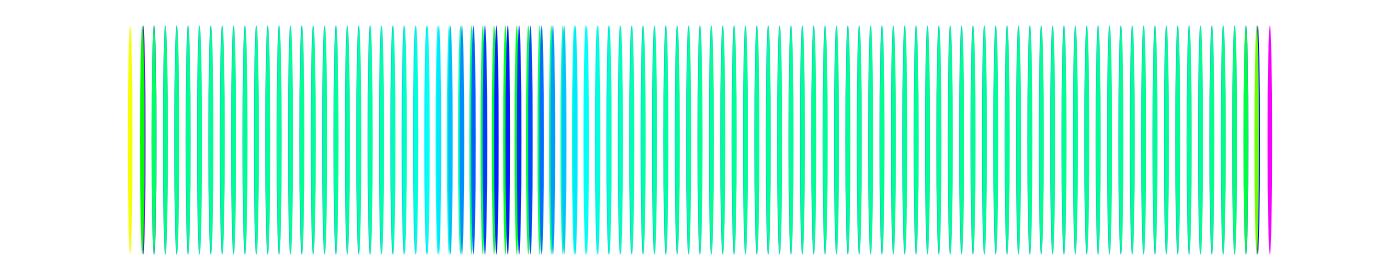

```mathematica
Graphics[{Hue[#2*10],Disk[{#1+#2/maxd,0},.4]}&@@@ls,ImageSize->1400]
```

```mathematica
lined=RandomReal[{0,20},200];
```

```mathematica
ListPlot[Array[#1^2-#1^3&,200,{-3.,3.}],PlotRange->All]
```

```mathematica
lined=Array[#1^2-#1^3&,200,{-3,3.}];
```

```mathematica
Manipulate[Show[{Graphics[{Hue[#2*10],Disk[{#1+#2/maxd,Array[#1^2-#1^3&,200,{-3,3.}][[#1]]},.4]}&@@@Transpose[{Range[200],phiToU[config[[k]]]}][[30;;150]]],Graphics[Line[{#1+#2/maxd,Array[#1^2-#1^3&,200,{-3,3.}][[#1]]}&@@@Transpose[{Range[200],phiToU[config[[k]]]}][[30;;150]]]]},ImageSize->1400],{k,1,100,1}]
```

```mathematica
Manipulate[Show[{Graphics[{Hue[#2*10],Disk[{#1+#2/maxd,If[Mod[#1,2]==0,0,1]},.4]}&@@@Transpose[{Range[200],phiToU[config[[k]]]}][[30;;150]]],Graphics[Line[{#1+#2/maxd,If[Mod[#1,2]==0,0,1]}&@@@Transpose[{Range[200],phiToU[config[[k]]]}][[30;;150]]]]},ImageSize->1400,Axes->True],{k,1,100,1}]
```

```mathematica
Manipulate[Graphics[{Hue[#2*10],Opacity[.6],Disk[{#1+#2/maxd,10*Sin[#1/10.]},1.]}&@@@Transpose[{Range[200],phiToU[config[[k]]]}][[30;;150]],ImageSize->700],{k,1,100,1}]
```

```mathematica
Manipulate[Graphics[{Hue[If[Mod[#1,2]==0,.30,.68]],Opacity[.6],Disk[{#1+#2/maxd,0},.4]}&@@@Transpose[{Range[200],phiToU[config[[k]]]}][[30;;150]],ImageSize->1400],{k,1,100,1}]
```

```mathematica
Graphics[{Hue[#1],Disk[]}]&/@{0.3,0.68}
```

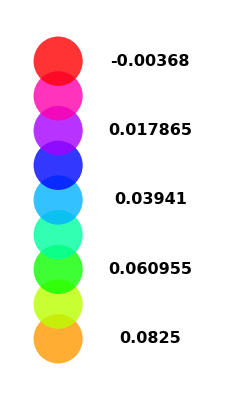

```mathematica
legd=Graphics[Array[{Hue[#1],Opacity[.8],Disk[{0,#1+10.},.08]}&,9,{0.1,1.}],Epilog->(Inset[Style[#1,Bold,16],#2]&@@@Transpose[{Array[#1&,5,Reverse@{-0.0036800,0.082500}],Array[{.3,#1}&,5,{10.1,11.}]}]),Axes->False,PlotRange->{{-.12,.5},All}]
```

```mathematica
legdevo=Graphics[Array[{Hue[#1],Opacity[.8],Rectangle[{0,#1+10.},{.2,#1+10.01}]}&,400,{-0.46,0.54}],Axes->False,Epilog->(Inset[Style[#1,Bold,20],#2]&@@@Transpose[{Array[#1&,5,{-0.09,0.09}],Array[{.5,#1}&,5,{9.55,10.5}]}]),PlotRange->{{-.12,.8},{9.4,10.6}}]
```

-Graphics-

```mathematica
Graphics[{Hue[5*#2],Disk[{#1+#2+65,5*Sin[(1#1)/4.9]-8+8},.4]}&@@@lss2,ImageSize->800,Axes->False]
```

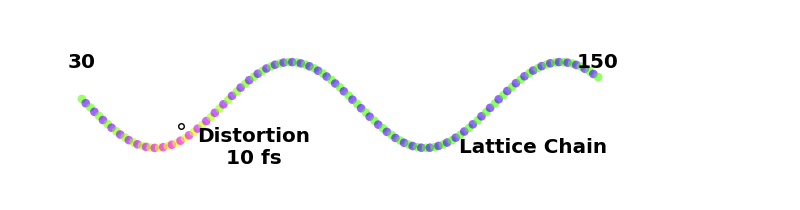

```mathematica
cf[1]=Graphics[{Hue[#2*5],Opacity[.6],Disk[{#1+#2,10*Sin[#1/10.]},1.]}&@@@Transpose[{Range[200],phiToU[config[[1]]]}][[30;;150]],ImageSize->800,Epilog->{Inset[Style["30",Bold,asize],{30.,10.}],Inset[Style["150",Bold,asize],{150.,10.}],Inset[legdevo,{165,0},Automatic,24],Inset[Style["Lattice Chain",Bold,asize],{135.,-10.}],Inset[Style["Distortion\n10 fs",Bold,asize],{70.,-10.}],Inset[Graphics[{Circle[{0,0},1]}],{53.,-5.},Automatic,30]},Axes->False,PlotRange->{{28,180},{-20,20}}]
```

```mathematica
bsize=20;
```

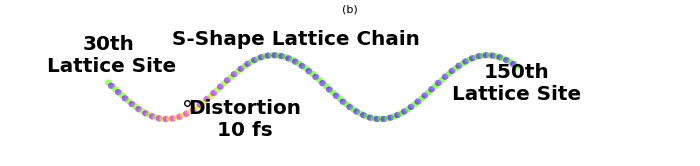

```mathematica
cf[1]=Graphics[{Hue[#2*5],Opacity[.6],Disk[{#1+#2,10*Sin[#1/10.]},1.]}&@@@Transpose[{Range[200],phiToU[config[[1]]]}][[30;;150]],ImageSize->700,Epilog->{Inset[legdevo,{172,0},Automatic,24],Inset[Style["30th\n Lattice Site",Bold,bsize],{30.,10.}],Inset[Style["150th\nLattice Site",Bold,bsize],{150.,1.}],Inset[Style["S-Shape Lattice Chain",Bold,bsize],{85.,15.}],Inset[Style["Distortion\n10 fs",Bold,bsize],{70.,-10.}],Inset[Graphics[{Circle[{0,0},1]}],{53.,-5.},Automatic,30]},Axes->False,PlotRange->{{17,185},{-20,20}},PlotLabel->Style["(b)",Bold,asize]]
```

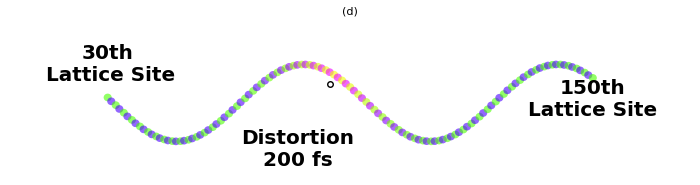

```mathematica
cf[2]=Graphics[{{Hue[#2*5],Opacity[.6],Disk[{#1+#2,10*Sin[#1/10.]},1.]}}&@@@Transpose[{Range[200],phiToU[config[[20]]]}][[30;;150]],ImageSize->700,Epilog->{Inset[Style["30th\n Lattice Site",Bold,bsize],{30.,10.}],Inset[Style["150th\nLattice Site",Bold,bsize],{150.,1.}],Inset[Style[" ",Bold,bsize],{135.,-10.}],Inset[Style["Distortion\n200 fs",Bold,bsize],{77.,-12.}],Inset[Graphics[{Circle[{0,0},1]}],{85.,5.},Automatic,30]},Axes->False,PlotRange->{{20,160},{-17,20}},PlotLabel->Style["(d)",Bold,asize]]
```

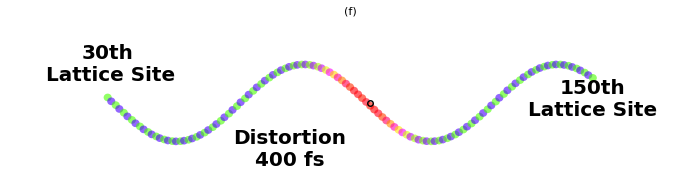

```mathematica
cf[3]=Graphics[{{Hue[#2*5],Opacity[.6],Disk[{#1+#2,10*Sin[#1/10.]},1.]}}&@@@Transpose[{Range[200],phiToU[config[[40]]]}][[30;;150]],ImageSize->700,Epilog->{Inset[Style["30th\n Lattice Site",Bold,bsize],{30.,10.}],Inset[Style["150th\nLattice Site",Bold,bsize],{150.,1.}],Inset[Style[" ",Bold,bsize],{135.,-10.}],Inset[Style["Distortion\n400 fs",Bold,bsize],{75.,-12.}],Inset[Graphics[{Circle[{0,0},1]}],{95.,-0.},Automatic,30]},Axes->False,PlotRange->{{20,160},{-17,20}},PlotLabel->Style["(f)",Bold,asize]]
```

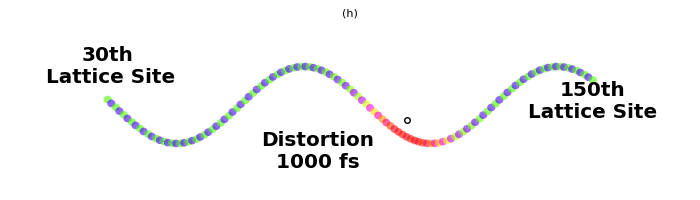

```mathematica
cf[4]=Graphics[{{Hue[#2*5],Opacity[.6],Disk[{#1+#2,10*Sin[#1/10.]},1.]}}&@@@Transpose[{Range[200],phiToU[config[[100]]]}][[30;;150]],ImageSize->700,Epilog->{Inset[Style["30th\n Lattice Site",Bold,bsize],{30.,10.}],Inset[Style["150th\nLattice Site",Bold,bsize],{150.,1.}],Inset[Style[" ",Bold,bsize],{135.,-10.}],Inset[Style["Distortion\n1000 fs",Bold,bsize],{82.,-12.}],Inset[Graphics[{Circle[{0,0},1]}],{104.,-4.},Automatic,30]},Axes->False,PlotRange->{{20,160},{-20,20}},PlotLabel->Style["(h)",Bold,asize]]
```

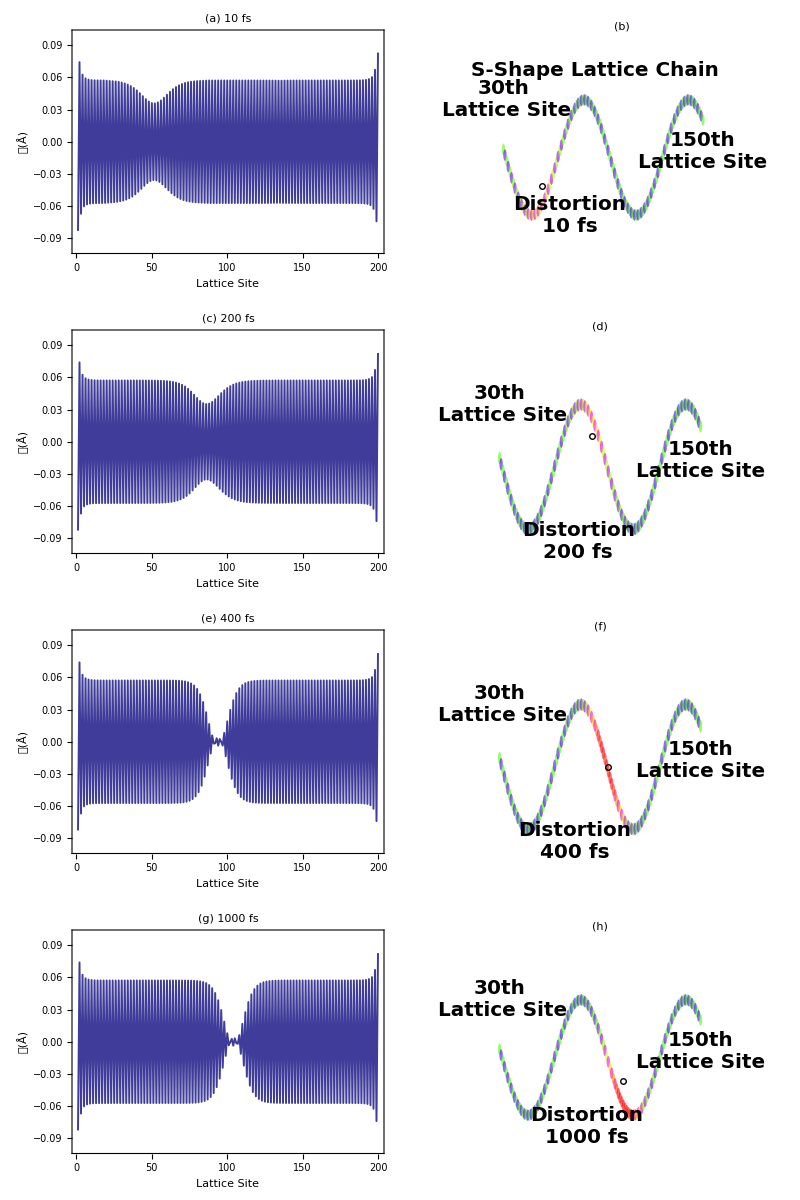

```mathematica
chf1=Grid[Transpose[{fa/@Range[4],cf/@Range[4]}]]
```

```mathematica
Export["chfigout.png",chf1,ImageResolution->300]
```

chfigout.png

```mathematica
Graphics[{Hue[#2*10],Opacity[.6],Disk[{#1+#2/maxd,0},1.]}&@@@Transpose[{Range[200],phiToU[config[[15]]]}][[30;;150]],ImageSize->700,Epilog->{Inset[Style["Distortion",Bold,20],{60.,-10.}],Inset[Graphics[{Circle[{0,0},1]}],{53.,-5.},Automatic,22]},Axes->True,PlotRange->{Automatic,{-17,12}}]
```

```mathematica
Graphics[Line[{#1+#2/maxd,lined[[#1]]}&@@@Transpose[{Range[200],phiToU[config[[10]]]}][[30;;150]]]]
```

```mathematica
Graphics[Line[Transpose[{Range[81],RandomReal[{0,20},81]}]]]
```

```mathematica
{Min@config[[100]],Max@config[[100]]}
```

```mathematica
legd=Graphics[Array[{Hue[#1],Opacity[.8],Disk[{0,#1+10.},.1]}&,9,{0.1,1.}],Epilog->(Inset[Style[#1,Bold,20],#2]&@@@Transpose[{Array[#1&,5,{-0.0036857251893759988,0.08251865132468744}],Array[{.3,#1}&,5,{10.1,11.}]}]),Axes->False,PlotRange->{{-.12,.5},All}]
```

```mathematica
{a1,a2}*{a3,a4}
```

```mathematica
config[[10]]*Array[If[Mod[#1,2]==0,1,-1]&,200,1]
```